Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

3.  Use of symmetry. Conclude from the boundary values in example 1 that u_21 = u_11 and u_22 = u_12. Show that this leads to a system of two equations and solve it.

The conclusion in the problem description is true because of left-right mirroring of boundary values, the only outside influences that can affect the problem. So only two equations need to be worked to get the whole layout. Having looked at the text answer, I can see that this is handled differently from the explanatory material in the text, so far as I can see. The point-centered cross discussed on p. 925 is dispensed with, and the arm leading toward the mirrored edge is ignored. With only three directions of influence for each active point, that will make the general matrix like

```mathematica
({{{{-3 Subscript[u, 11], Subscript[u, 12], Subscript[P, 01], Subscript[P, 10]}}}, {{{Subscript[u, 11], -3 Subscript[u, 12], Subscript[P, 02], Subscript[P, 13]}}}})
```

And after inserting boundary values

```mathematica
({{{{-3 Subscript[u, 11], Subscript[u, 12], 100, 100}}}, {{{Subscript[u, 11], -3 Subscript[u, 12], 100, 0}}}})
```

The augmented section is broken off into a separate vector.

```mathematica
rh=({{-200}, {-100}})
```

{{-200},{-100}}

And the un-augmented section is filled with coefficients.

```mathematica
aa=({{-3, 1}, {1, -3}})
```

{{-3,1},{1,-3}}

The system can be solved, although the text answer does not bother with this part.

```mathematica
LinearSolve[aa,rh]
```

{{175/2},{125/2}}

And the system of points or nodes on the other side of the mirror line has the same value as their analogous points. The slightly mysterious ground covered by this particular problem is not generalized nor revisited during the remainder of the section work.

5 - 10 Gauss elimination, Gauss-Seidel iteration
For the grid in the figure below, compute the potential at the four internal points by Gauss and by 5 Gauss-Seidel steps with starting values 100, 100, 100, 100 if the boundary values on the edges are:

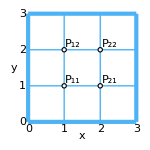

```mathematica
kru=RGBColor[0.3,0.7,0.96];
innerbw=RGBColor[.97,.97,.994];Graphics[{{kru,Thickness[0.02],Line[{{0,0},{0,3}}]},{kru, Thickness[0.02],Line[{{0,0},{3,0}}]},{kru,Thickness[0.02],Line[{{3,0},{3,3}}]},{kru,Thickness[0.02],Line[{{0,3},{3,3}}]},{kru,Line[{{0,1},{3,1}}]},{kru,Line[{{0,2},{3,2}}]},{kru,Line[{{1,0},{1,3}}]},{kru,Line[{{2,0},{2,3}}]},{Text[Style["1",Medium],{1,-0.2}]},{Text[Style["2",Medium],{2,-0.2}]},{Text[Style["3",Medium],{3,-0.2}]},{Text[Style["0",Medium],{-0.15,0}]},{Text[Style["1",Medium],{-0.15,1}]},{Text[Style["2",Medium],{-0.15,2}]},{Text[Style["3",Medium],{-0.15,3}]},{Text[Style["0",Medium],{0.03,-0.2}]},{Text[Style["x",Medium],{1.5,-0.4}]},{Text[Style["y",Medium],{-0.4,1.5}]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,1},0.06]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,2},0.06]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,1},0.06]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,2},0.06]},{Text[Style["P_11",Medium],{1.25,1.15}]},{Text[Style["P_21",Medium],{2.25,1.15}]},{Text[Style["P_12",Medium],{1.25,2.15}]},{Text[Style["P_22",Medium],{2.25,2.15}]}},ImageSize->150]
```

5. u(1, 0) = 60, u(2, 0) = 300, u = 100 on the other three edges.

Mathematica can solve this easily if the matrices can be decoded properly. In this problem numbered line (11) on p. 926 figures strongly, as well as example 1 on the same page. On p. 925 the concept of cardinal directions is discussed, and these figure into the idea of node location. The objective will be to integrate the four points (or nodes) P_11, P_21, P_12, and P_22, in that order, into a systematic grid. The points are connected to each other by edges, but they also have cardinal edges which are not attached to any of the other three points, and because these are connected to the outer boundary, these peripheral cardinal edges are associated with weights, values, charges, or temperatures. Numbered line (11) looks like this: u_(i+1,j) + u_(i,j+1) + u_(i-1,j) + u_(i,j-1) -4 u_ij = 0. The i and j in the subscripts relate to the P_ij mentioned before. I notice that the -4 term is the only one without plus signs or minus signs. These -4 terms will form the diagonal of the un-augmented matrix, which I can already build.

```mathematica
({{-4 Subscript[u, 11], □, □, □, □, □}, {□, -4 Subscript[u, 21], □, □, □, □}, {□, □, -4 Subscript[u, 12], □, □, □}, {□, □, □, -4 Subscript[u, 22], □, □}})
```

The subscripts of the entries in the skeleton matrix define and identify the column subscripts, for the left four columns. According to numbered line (11), each socket in the matrix is composed of an equation containing five factors. Referring to the skeleton matrix and the node position diagram above, I can fill these in, examining the connecting edges of each node to see what may be attached. The right two columns collect external edges, and their subscripts are not ordered.

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], Subscript[u, 12], □, Subscript[u, 10], Subscript[u, 01]}, {Subscript[u, 11], -4 Subscript[u, 21], □, Subscript[u, 22], Subscript[u, 20], Subscript[u, 31]}, {Subscript[u, 11], □, -4 Subscript[u, 12], Subscript[u, 22], Subscript[u, 13], Subscript[u, 02]}, {□, Subscript[u, 21], Subscript[u, 12], -4 Subscript[u, 22], Subscript[u, 23], Subscript[u, 32]}});
```

Now that I have the positions filled in, I can look at the right two columns to see what contributions the outside edges are making to each line.

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], Subscript[u, 12], □, 60, 100}, {Subscript[u, 11], -4 Subscript[u, 21], □, Subscript[u, 22], 300, 100}, {Subscript[u, 11], □, -4 Subscript[u, 12], Subscript[u, 22], 100, 100}, {□, Subscript[u, 21], Subscript[u, 12], -4 Subscript[u, 22], 100, 100}});
```

As the right two columns are carried across the equals sign, a sign change takes place, and they transform into a vector.

```mathematica
rh=({{-160}, {-400}, {-200}, {-200}});
```

Looking at the remaining four columns, all I care about now are the coefficients.

```mathematica
aey =({{-4, 1, 1, 0}, {1, -4, 0, 1}, {1, 0, -4, 1}, {0, 1, 1, -4}});
```

And at this point I am ready to solve the system.

```mathematica
LinearSolve[aey,rh]
```

{{105},{155},{105},{115}}

7.  U_0 on the upper and lower edges, -U_0 on the left and right. Sketch the equipotential lines.

For this problem I can skip one step and start with

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], Subscript[u, 12], □, Subscript[u, 10], Subscript[u, 01]}, {Subscript[u, 11], -4 Subscript[u, 21], □, Subscript[u, 22], Subscript[u, 20], Subscript[u, 31]}, {Subscript[u, 11], □, -4 Subscript[u, 12], Subscript[u, 22], Subscript[u, 13], Subscript[u, 02]}, {□, Subscript[u, 21], Subscript[u, 12], -4 Subscript[u, 22], Subscript[u, 23], Subscript[u, 32]}});
```

Each node has an edge with connects with left or right boundary, and also an edge which connects with top or bottom. So I get

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], Subscript[u, 12], □, Subscript[U, 0], -Subscript[U, 0]}, {Subscript[u, 11], -4 Subscript[u, 21], □, Subscript[u, 22], Subscript[U, 0], -Subscript[U, 0]}, {Subscript[u, 11], □, -4 Subscript[u, 12], Subscript[u, 22], Subscript[U, 0], -Subscript[U, 0]}, {□, Subscript[u, 21], Subscript[u, 12], -4 Subscript[u, 22], Subscript[U, 0], -Subscript[U, 0]}});
```

```mathematica
rh0=({{0}, {0}, {0}, {0}});
```

```mathematica
LinearSolve[aey,rh0]
```

{{0},{0},{0},{0}}

Below is my poor attempt at sketching equipotential lines, or regions.

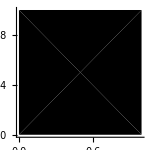

```mathematica
Graphics[{{Polygon[{{0,0},{1,0},{0.5,0.5},{0,0}},VertexColors->{Red,Red,White}]},{Polygon[{{0,1},{0.5,0.5},{1,1},{0,1}},VertexColors->{Red,White,Red}]},{Polygon[{{0,0},{0.5,0.5},{0,1},{0,0}},VertexColors->{RGBColor[0.7,0.7,0.2],White,RGBColor[1,0.7,0.1]}]},{Polygon[{{1,0},{1,1},{0.5,0.5}},VertexColors->{RGBColor[0.7,0.7,0.2],RGBColor[1,0.7,0.1],White}]}},AspectRatio->Automatic,Axes->True, ImageSize->150]
```

9.  u = Sin[1/3π x] on the upper edge, 0 on the other edges.

Once again I can skip one step and start with

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], Subscript[u, 12], □, Subscript[u, 10], Subscript[u, 01]}, {Subscript[u, 11], -4 Subscript[u, 21], □, Subscript[u, 22], Subscript[u, 20], Subscript[u, 31]}, {Subscript[u, 11], □, -4 Subscript[u, 12], Subscript[u, 22], Subscript[u, 13], Subscript[u, 02]}, {□, Subscript[u, 21], Subscript[u, 12], -4 Subscript[u, 22], Subscript[u, 23], Subscript[u, 32]}});
```

And then fill in the values added by external edges, minding the x value of source.

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], Subscript[u, 12], □, 0, 0}, {Subscript[u, 11], -4 Subscript[u, 21], □, Subscript[u, 22], 0, 0}, {Subscript[u, 11], □, -4 Subscript[u, 12], Subscript[u, 22], Sin[1/3 π ], 0}, {□, Subscript[u, 21], Subscript[u, 12], -4 Subscript[u, 22], Sin[1/3 π 2], 0}});
```

And make the vector on rhs, remembering the sign change.

```mathematica
rh1=({{0}, {0}, {-Sin[1/3 π 1]}, {-Sin[1/3 π 2]}});
```

```mathematica
LinearSolve[aey,rh1]
```

{{(√3)/16},{(√3)/16},{(3 √3)/16},{(3 √3)/16}}

```mathematica
NumberForm[%,{6,6}]
```

{{0.108253},{0.108253},{0.324760},{0.324760}}

The green cell above matches the answer in the text.

11.  Find the potential in the figure below using (a) the coarse grid, (b) the fine grid 5 × 3, and Gauss elimination. Hint. In (b), use symmetry; take u = 0 as boundary value at the two points at which the potential has a jump.

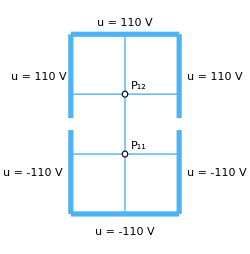

```mathematica
kru=RGBColor[0.3,0.7,0.96];
innerbw=RGBColor[.97,.97,.994];g1=Graphics[{{kru,Thickness[0.015],Line[{{0,0},{0,1.4}}]},{kru,Thickness[0.015],Line[{{0,1.6},{0,3}}]},{kru, Thickness[0.015],Line[{{0,0},{2,0}}]},{kru,Thickness[0.015],Line[{{2,0},{2,1.4}}]},{kru,Thickness[0.015],Line[{{2,1.6},{2,3}}]},{kru,Thickness[0.015],Line[{{0,3},{2,3}}]},{kru,Line[{{0,1},{2,1}}]},{kru,Line[{{0,2},{2,2}}]},{kru,Line[{{1,0},{1,3}}]},{Text[Style["u = -110 V",Medium],{1,-0.28}]},{Text[Style["u = -110 V",Medium],{-0.7,0.7}]},{Text[Style["u = 110 V",Medium],{1,3.2}]},{Text[Style["u = 110 V",Medium],{-0.6,2.3}]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,1},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,2},0.05]},{Text[Style["P_11",Medium],{1.25,1.15}]},{Text[Style["u = -110 V",Medium],{2.7,0.7}]},{Text[Style["P_12",Medium],{1.25,2.15}]},{Text[Style["u = 110 V",Medium],{2.65,2.3}]}},ImageSize->250]
```

part (a)

With only two nodes, the system simplifies. Numbered line (11) still holds, even though it will be a 4-column matrix with 2 rows, like

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 12], Subscript[u, 01], Subscript[u, 10], Subscript[u, 21]}, {Subscript[u, 11], -4 Subscript[u, 12], Subscript[u, 02], Subscript[u, 13], Subscript[u, 22]}})
```

And the total matrix will be like

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 12], -110, -110, -110}, {Subscript[u, 11], -4 Subscript[u, 12], 110, 110, 110}})
```

with the right vector equal to

```mathematica
rh4={{330},{-330}}
```

{{330},{-330}}

and the left matrix equal to

```mathematica
ae4={{-4,1},{1,-4}}
```

{{-4,1},{1,-4}}

```mathematica
LinearSolve[ae4,rh4]
```

{{-66},{66}}

part (b) (note: some node identifiers have been left blank to save space)

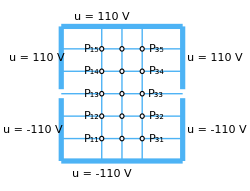

```mathematica
kru=RGBColor[0.3,0.7,0.96];
innerbw=RGBColor[.97,.97,.994];g2=Graphics[{{kru,Thickness[0.015],Line[{{0,0},{0,1.4}}]},{kru,Thickness[0.015],Line[{{0,1.6},{0,3}}]},{kru, Thickness[0.015],Line[{{0,0},{3,0}}]},{kru, ,Line[{{1.5,0},{1.5,3}}]},{kru,Thickness[0.015],Line[{{3,0},{3,1.4}}]},{kru,Thickness[0.015],Line[{{3,1.6},{3,3}}]},{kru,Thickness[0.015],Line[{{0,3},{3,3}}]},{kru,Line[{{0,1},{3,1}}]},{kru,Line[{{0,2},{3,2}}]},{kru,Line[{{1,0},{1,3}}]},{kru,Line[{{0,1.5},{3,1.5}}]},{kru,Line[{{2,0},{2,3}}]},{kru,Line[{{0,2.5},{3,2.5}}]},{kru,Line[{{0,0.5},{3,0.5}}]},{Text[Style["u = -110 V",Medium],{1,-0.28}]},{Text[Style["u = -110 V",Medium],{-0.7,0.7}]},{Text[Style["u = 110 V",Medium],{1,3.2}]},{Text[Style["u = 110 V",Medium],{-0.6,2.3}]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,1},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,2},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,1},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,2},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,1.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,1.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,0.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1.5,0.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1.5,1},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1.5,1.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1.5,2},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1.5,2.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,0.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,2.5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,2.5},0.05]},{Text[Style["P_11",Medium],{0.75,0.5}]},{Text[Style["P_13",Medium],{0.75,1.5}]},{Text[Style["P_14",Medium],{0.75,2}]},{Text[Style["P_15",Medium],{0.75,2.5}]},{Text[Style["P_31",Medium],{2.35,0.5}]},{Text[Style["P_32",Medium],{2.35,1}]},{Text[Style["P_33",Medium],{2.35,1.5}]},{Text[Style["P_34",Medium],{2.35,2}]},{Text[Style["P_35",Medium],{2.35,2.5}]},{Text[Style["u = -110 V",Medium],{3.85,0.7}]},{Text[Style["P_12",Medium],{0.75,1}]},{Text[Style["u = 110 V",Medium],{3.8,2.3}]}},ImageSize->250]
```

Okay, in this part the problem description is going to lay down some ground rules. That is, the points P_13, P_23, P_33 are going to be taken to equal zero. In other words, the line that these three nodes stand on is like a zero boundary edge. Then for example P_11, P_21, P_31,P_12, P_22,P_32 will be the system I will look at, the lower node system. And because of symmetry, the solution will equal the minus of the upper sextet of points. So I can go ahead and use the matrix, modified for 6 × 6.

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], □, Subscript[u, 12], □, □, -110, -110}, {Subscript[u, 11], -4 Subscript[u, 21], Subscript[u, 31], □, Subscript[u, 22], □, -110, □}, {□, Subscript[u, 21], -4 Subscript[u, 31], □, □, Subscript[u, 32], -110, -110}, {Subscript[u, 11], □, □, -4 Subscript[u, 12], Subscript[u, 22], □, -110, 0}, {□, Subscript[u, 21], □, Subscript[u, 12], -4 Subscript[u, 22], Subscript[u, 32], 0, □}, {□, □, Subscript[u, 31], □, Subscript[u, 22], -4 Subscript[u, 32], 0, -110}})
```

Pulling the right two columns across,

```mathematica
rhb=({{220}, {110}, {220}, {110}, {0}, {110}})
```

{{220},{110},{220},{110},{0},{110}}

Leaving

```mathematica
ae6=({{-4, 1, 0, 1, 0, 0}, {1, -4, 1, 0, 1, 0}, {0, 1, -4, 0, 0, 1}, {1, 0, 0, -4, 1, 0}, {0, 1, 0, 1, -4, 1}, {0, 0, 1, 0, 1, -4}})
```

{{-4,1,0,1,0,0},{1,-4,1,0,1,0},{0,1,-4,0,0,1},{1,0,0,-4,1,0},{0,1,0,1,-4,1},{0,0,1,0,1,-4}}

Followed by the operation

```mathematica
LinearSolve[ae6,rhb]
```

{{-14960/161},{-14080/161},{-14960/161},{-10340/161},{-8690/161},{-10340/161}}

```mathematica
NumberForm[%,{4,2}]
```

{{-92.92},{-87.45},{-92.92},{-64.22},{-53.98},{-64.22}}

The above cell matches the text answer. To find out the solution value for a specific u_xx, follow the matrix diagonal down to its position.

13. For the square 0 ≤ x ≤ 4, 0 ≤ y ≤ 4 let the boundary temperatures be 0 ℃ on the horizontal and 50 ℃ on the vertical edges. Find the temperatures at the interior points of a square grid with h = 1.

Apparently the requirement that h = 1 means that there will be nine points.

```mathematica
({{-4 Subscript[u, 11], Subscript[u, 21], □, Subscript[u, 12], □, □, □, □, □, 50, 0}, {Subscript[u, 11], -4 Subscript[u, 21], Subscript[u, 31], □, Subscript[u, 22], □, □, □, □, 0, □}, {□, Subscript[u, 21], -4 Subscript[u, 31], □, □, Subscript[u, 32], □, □, □, 50, 0}, {Subscript[u, 11], □, □, -4 Subscript[u, 12], Subscript[u, 22], □, Subscript[u, 13], □, □, 50, □}, {□, Subscript[u, 21], □, Subscript[u, 12], -4 Subscript[u, 22], Subscript[u, 32], □, Subscript[u, 23], □, □, □}, {□, □, Subscript[u, 31], □, Subscript[u, 22], -4 Subscript[u, 32], □, □, Subscript[u, 33], 50, □}, {□, □, □, Subscript[u, 12], □, □, -4 Subscript[u, 13], Subscript[u, 23], □, 0, 50}, {□, □, □, □, Subscript[u, 22], □, Subscript[u, 13], -4 Subscript[u, 23], Subscript[u, 33], 0, □}, {□, □, □, □, □, Subscript[u, 32], □, Subscript[u, 23], -4 Subscript[u, 33], 0, 50}});
```

```mathematica
a911=({{-4, 1, 0, 1, 0, 0, 0, 0, 0}, {1, -4, 1, 0, 1, 0, 0, 0, 0}, {0, 1, -4, 0, 0, 1, 0, 0, 0}, {1, 0, 0, -4, 1, 0, 1, 0, 0}, {0, 1, 0, 1, -4, 1, 0, 1, 0}, {0, 0, 1, 0, 1, -4, 0, 0, 1}, {0, 0, 0, 1, 0, 0, -4, 1, 0}, {0, 0, 0, 0, 1, 0, 1, -4, 1}, {0, 0, 0, 0, 0, 1, 0, 1, -4}});
```

```mathematica
r911=({{-50}, {0}, {-50}, {-50}, {0}, {-50}, {-50}, {0}, {-50}});
```

```mathematica
LinearSolve[a911,r911]
```

{{25},{75/4},{25},{125/4},{25},{125/4},{25},{75/4},{25}}

```mathematica
N[NumberForm[%,{4,2}]]
```

NumberForm::iprf: Formatting specification {4.,2.} should be a positive integer or a pair of positive integers.

{{25.},{18.75},{25.},{31.25},{25.},{31.25},{25.},{18.75},{25.}}

The answer in the green cell above matches the answer in the text.

15.  Find the isotherms for the square and grid in problem 13 if u = Sin[1/4π x] on the horizontal and -Sin[1/4π y] on the vertical edges. Try to sketch some isotherms.

The plot that I come up with is somewhat fanciful. I have no guidance on the mode of temperature dissipation, and just tried to put something down. The problem description for the function for describing the isotherms on the vertical does not seem right, and I dropped the sign in order to show an effect from both axes in the same quadrant. Other than that, I decided to keep the sine functions the same, although compressing the coefficient might have made it look more realistic.

```mathematica
N[Log[9]]
```

2.19722

```mathematica
arc=N[Table[ⅇ^(-0.2x),{x,1,15}]]
```

{0.818731,0.67032,0.548812,0.449329,0.367879,0.301194,0.246597,0.201897,0.165299,0.135335,0.110803,0.090718,0.0742736,0.0608101,0.0497871}

```mathematica
arc1=N[Table[ⅇ^x,{x,-3,2.2,0.2}]]
```

{0.0497871,0.0608101,0.0742736,0.090718,0.110803,0.135335,0.165299,0.201897,0.246597,0.301194,0.367879,0.449329,0.548812,0.67032,0.818731,1.,1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552,4.95303,6.04965,7.38906,9.02501}

```mathematica
p1=Plot[Table[{arc1[[n]]Sin[1/4 π x]},{n,1,26}],{x,0,2 π},PlotStyle->{Blue,Thickness[0.002]},ImageSize->300,AspectRatio->Automatic,Axes->True, GridLines->Automatic,PlotRange->{{0,6},{0,6}}];
```

```mathematica
p1u=Plot[Table[{-arc1[[n]]Sin[1/4 π x]+6},{n,1,26}],{x,0,4},PlotStyle->{Green,Thickness[0.002]},ImageSize->300,AspectRatio->Automatic,Axes->True, GridLines->Automatic,PlotRange->{{0,5.5},{0,6}}];
```

```mathematica
p2=Plot[Table[{arc1[[n]]Sin[1/4 π x]},{n,1,26}],{x,0,3},PlotStyle->{Red,Thickness[0.002]},ImageSize->150,AspectRatio->Automatic,PlotRange->{{0,3},{0,5.5}}];
```

```mathematica
p2u=Plot[Table[{arc1[[n]]Sin[1/4 π (x+2)]+4},{n,1,26}],{x,3,6},PlotStyle->{RGBColor[0.9,0.9,0.2],Thickness[0.002]},ImageSize->150,AspectRatio->Automatic,PlotRange->{{0,6},{0,6}}];
```

The following axisFlip code was obtained at https://mathematica.stackexchange.com/questions/18655/how-can-i-transpose-x-and-y-axis-on-a-plot, from a response by Mr. Wizard.

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
```

```mathematica
p4= p2 // axisFlip;
p5= p2u // axisFlip ;
```

```mathematica
innerbw=RGBColor[.97,.97,.994];
```

```mathematica
p3=Graphics[{{Opacity[0.3],RGBColor[0.9,0.9,0.9],Rectangle[{-0.5,-0.5},{6.5,6.5}]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,2},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,4},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{3,2},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{3,4},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{3,3},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,3},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,1},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,1},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,2},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,3},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,4},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{3,1},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{3,5},0.05]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,5},0.05]}},Axes->True,GridLines->Automatic,AspectRatio->Automatic];
```

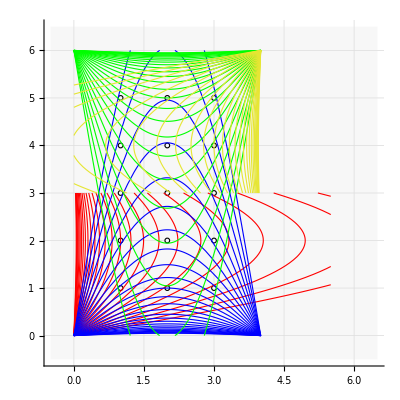

```mathematica
Show[p3,p4,p1,p1u,p5]
```

17.  What p_0 in (18) should we choose for problem 16? Apply the ADI formulas (17) with that value of p_0 to problem 16, performing 1 step. Illustrate the improved convergence by comparing with the corresponding values 0.077, 0.308 after the first step in problem 16. (Use the starting values zero.)

Numbered line (18) on p. 930 is p_0 = 2 Sin[π/K]. After referring to problem 16, I see that this problem is actually a revisitation of problem 9, a problem I have already done. Let me bring that figure here. The goal of the problem is to compute the potential at the four internal points. The boundary value for the top edge is Sin[1/3π x], and the other three edges are zero. If a starting value is to be used, the text recommends 100 for all four points.

```mathematica
kru=RGBColor[0.3,0.7,0.96];
innerbw=RGBColor[.97,.97,.994];Graphics[{{kru,Thickness[0.02],Line[{{0,0},{0,3}}]},{kru, Thickness[0.02],Line[{{0,0},{3,0}}]},{kru,Thickness[0.02],Line[{{3,0},{3,3}}]},{kru,Thickness[0.02],Line[{{0,3},{3,3}}]},{kru,Line[{{0,1},{3,1}}]},{kru,Line[{{0,2},{3,2}}]},{kru,Line[{{1,0},{1,3}}]},{kru,Line[{{2,0},{2,3}}]},{Text[Style["1",Medium],{1,-0.2}]},{Text[Style["2",Medium],{2,-0.2}]},{Text[Style["3",Medium],{3,-0.2}]},{Text[Style["0",Medium],{-0.15,0}]},{Text[Style["1",Medium],{-0.15,1}]},{Text[Style["2",Medium],{-0.15,2}]},{Text[Style["3",Medium],{-0.15,3}]},{Text[Style["0",Medium],{0.03,-0.2}]},{Text[Style["x",Medium],{1.5,-0.4}]},{Text[Style["y",Medium],{-0.4,1.5}]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,1},0.06]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,2},0.06]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,1},0.06]},{EdgeForm[Directive[Black]],innerbw,Disk[{2,2},0.06]},{Text[Style["P_11",Medium],{1.25,1.15}]},{Text[Style["P_21",Medium],{2.25,1.15}]},{Text[Style["P_12",Medium],{1.25,2.15}]},{Text[Style["P_22",Medium],{2.25,2.15}]}},ImageSize->150]
```

-Graphics-

First I will write the equation the simple way. Just the Laplace and the boundary conditions.

```mathematica
eqn=D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0;
bc={u[0,y]==0,u[3,y]==0,u[x,0]==0,u[x,3]==Sin[1/3 π x]};
```

The presence of the enhancers does not really make a difference in the output of NDSolveValue, and I could have left them out.

```mathematica
uso=NDSolveValue[{eqn,bc},u,{x,0,3},{y,0,3},PrecisionGoal->8,AccuracyGoal->8,WorkingPrecision->10, MaxSteps->∞]
```

InterpolatingFunction[{{0., 3.}, {0., 3.}}, <>]

The following table gives the values of the Interpolating function at the nodes of interest.

```mathematica
Table[uso[n,m],{n,1,2},{m,1,2}]
```

{{0.09369,0.299845},{0.09369,0.299845}}

The text answer lists a couple of successive iterations. As shown below, they lie in the neighborhood of the results from NDSolve. Both the NDSolve results and the text answer are repetitious, between u_21= u_21 and u_12= u_22.

```mathematica
Grid[{{Coarse ADI,"4S"},{0.0849,0.3170},{0.1083,0.3248}},Frame->All]
```

ADI Coarse | 4S
0.0849 | 0.317
0.1083 | 0.3248

Now I will express the function as a somewhat more involved expression, which, however, comes up with the same output values as the simple version above. Somewhere on the web I read that Dirichlet conditions are intended to be applied at a point instead of an edge. However, it appears that in the following form, the conditions can overcome that limitation.

```mathematica
soll=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==0,DirichletCondition[u[x,y]==Sin[(π x)/3],y==3&&0≤x≤3],DirichletCondition[u[x,y]==0,y==0&&0≤x≤3],DirichletCondition[u[x,y]==0,x==0&&0≤y≤3],DirichletCondition[u[x,y]==0,x==3&&0≤y≤3]},u,{x,0,3},{y,0,3},PrecisionGoal->16,AccuracyGoal->16,WorkingPrecision->18, MaxSteps->∞]
```

InterpolatingFunction[{{0., 3.}, {0., 3.}}, <>]